```mathematica
assumptions={α∈Reals,β∈Reals,α^2+β^2==1,ω∈Reals,ℰ∈Reals,σ>0};
𝒮[x_]:=Simplify[x,assumptions];
ℱ𝒮[x_]:=FullSimplify[x,assumptions];

𝒩Dist[σ_]:=NormalDistribution[0,σ];
𝒰Dist[σ_]:=UniformDistribution[{-Sqrt[3]σ,Sqrt[3]σ}];
𝒜Dist[σ_]:=ArcSinDistribution[{-Sqrt[2]σ,Sqrt[2]σ}];
ProbAllZero𝒩[σ_,ω_,ℰ_]:=1/2(1+ⅇ^(-1/2 σ^2(ℰ-ω)^2));
ProbAllZero𝒰[σ_,ω_,ℰ_]:=1/2(1+Sinc[√3 σ(ℰ-ω)]);
ProbAllZero𝒜[σ_,ω_,ℰ_]:=1/2(1+BesselJ[0,√2 σ(ℰ-ω)]);
probAllZeroDict=Association[{𝒩Dist->ProbAllZero𝒩,𝒰Dist->ProbAllZero𝒰,𝒜Dist->ProbAllZero𝒜}];
ProbAllZeroGM[dist_,σ_,ω_,ℰ_]:=Exp[NIntegrate[PDF[dist[σ],t]Log[(1+Cos[t(ℰ-ω)])/2],{t,-∞,∞},MaxRecursion->20,Method->{"SymbolicDomainDecomposition",Method->{"LocalAdaptive",MinRecursion->10}}]];
ProbAllZeroGM𝒩[σ_,ω_,ℰ_]:=ProbAllZeroGM[𝒩Dist,σ,ω,ℰ];
ProbAllZeroGM𝒰[σ_,ω_,ℰ_]:=ProbAllZeroGM[𝒰Dist,σ,ω,ℰ];
ProbAllZeroGM𝒜[σ_,ω_,ℰ_]:=ProbAllZeroGM[𝒜Dist,σ,ω,ℰ];
probAllZeroGMDict=Association[{𝒩Dist->ProbAllZeroGM𝒩,𝒰Dist->ProbAllZeroGM𝒰,𝒜Dist->ProbAllZeroGM𝒜}];
```

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
RodeoPlotStyleSequence[ylabel_]:=Sequence[Filling->None,PlotRange->{0,1},AxesLabel->{"ℰ",ylabel},TicksStyle->Directive[FontOpacity->1,FontSize->8]];

ProbAllZeroExpectation[dist_,σ_,n_,ω_,ℰ_,α_,β_]:=α^2 probAllZeroDict[dist][σ,ω,ℰ]^n+β^2 probAllZeroDict[dist][σ,-ω,ℰ]^n;
ProbAllZeroExpectationGM[dist_,σ_,n_,ω_,ℰ_,α_,β_]:=α^2 probAllZeroGMDict[dist][σ,ω,ℰ]^n+β^2 probAllZeroGMDict[dist][σ,-ω,ℰ]^n;

SingleRunAllZero[dist_,σ_,n_,ω_,ℰ_,α_,β_,shots_]:=RandomVariate[BinomialDistribution[shots,ProbAllZeroExpectation[dist,σ,n,ω,ℰ,α,β]]]/shots;
RodeoAllZeroExpectationPlot[dist_,σ_,n_,ω_,α_,β_,min_,max_,join_,color_]:=Plot[ProbAllZeroExpectation[dist,σ,n,ω,ℰ,α,β] ,{ℰ,min,max},Evaluate[RodeoPlotStyleSequence["(P̄)_n"]],PlotStyle->{Thin,color}];

TimeArray[dist_,σ_,n_]:=Table[RandomVariate[dist[σ]],{k,1,n}];
ProbPlus[n_,ω_,ℰ_,α_,β_,timearray_]:=1/(1+(β/α)^2 Product[(1+Cos[timearray[[k]](ℰ+ω)])/(1+Cos[timearray[[k]](ℰ-ω)]),{k,1,n}]);
ProbMinus[n_,ω_,ℰ_,α_,β_,timearray_]:=1/(1+(α/β)^2 Product[(1+Cos[timearray[[k]](ℰ-ω)])/(1+Cos[timearray[[k]](ℰ+ω)]),{k,1,n}]);
SingleRunPlusOverlap[probability_,shots_]:=RandomVariate[BinomialDistribution[shots,probability]]/shots;

Needs["ErrorBarPlots`"];
RodeoPlusOverlapPoint[dist_,σ_,n_,ω_,ℰ_,α_,β_,evalreps_,errorbars_]:=With[{data=Table[ProbPlus[n,ω,ℰ,α,β,TimeArray[dist,σ,n]],{k,1,evalreps}]},With[{mean=Mean[data]},If[errorbars,{{ℰ,mean},ErrorBar[Quantile[data,{1/4,3/4}]-{mean,mean}]},{ℰ,mean}]]]
RodeoPlusOverlapPlot[dist_,σ_,n_,ω_,α_,β_,evalreps_,min_,max_,diff_,join_,color_,errorbars_]:=With[{points=Table[RodeoPlusOverlapPoint[dist,σ,n,ω,ℰ,α,β,evalreps,errorbars],{ℰ,min,max,diff}]},If[errorbars,ErrorListPlot,ListPlot][points,Evaluate[RodeoPlotStyleSequence["OverBar[√(1 - SuperscriptBox[Δ, 2])]"]],Joined->join,PlotStyle->{Thin,color}]];
RodeoPlusLogResidualPoint[dist_,σ_,n_,ω_,ℰ_,α_,β_,evalreps_]:=With[{data=Table[Log[Sqrt[ProbMinus[n,ω,ℰ,α,β,TimeArray[dist,σ,n]]]],{k,1,evalreps}]},With[{mean=Mean[data]},{ℰ,mean}]]
RodeoPlusLogResidualPlot[dist_,σ_,n_,ω_,α_,β_,evalreps_,min_,max_,diff_,join_,color_]:=With[{points=Table[RodeoPlusLogResidualPoint[dist,σ,n,ω,ℰ,α,β,evalreps],{ℰ,min,max,diff}]},ListPlot[points,Filling->None,AxesLabel->{"ℰ","ln[Δ̄]"},TicksStyle->Directive[FontOpacity->1,FontSize->8],Joined->join,PlotStyle->{Thin,color}]];

ProbPlusExpectation[dist_,σ_,n_,ω_,ℰ_,α_,β_,mr_,pg_]:=Re[NIntegrate[Product[PDF[dist[σ],Subscript[t, k]],{k,1,n}]/(1+(β/α)^2 Product[(1+Cos[Subscript[t, k](ℰ+ω)])/(1+Cos[Subscript[t, k](ℰ-ω)]),{k,1,n}]),Table[Subscript[t, k],{k,1,n}]∈FullRegion[n],MaxRecursion->mr,PrecisionGoal->pg,Method->{"SymbolicDomainDecomposition",Method->{"LocalAdaptive",MinRecursion->Quotient[mr,2]}}]];

ProbMinusExpectation[dist_,σ_,n_,ω_,ℰ_,α_,β_,mr_,pg_]:=1-ProbPlusExpectation[dist,σ,n,ω,ℰ,α,β,mr,pg];
RodeoPlusOverlapExpectationPlot[dist_,σ_,n_,ω_,α_,β_,min_,max_,diff_,join_,color_,mr_,pg_]:=DiscretePlot[ProbPlusExpectation[dist,σ,n,ω,ℰ,α,β,mr,pg] ,{ℰ,min,max,diff},Evaluate[RodeoPlotStyleSequence["(P̄)_n"]],Joined->join,PlotStyle->{Thin,color}];
RodeoCombinedExpectationPlot[dist_,σ_,n_,ω_,α_,β_,min_,max_,diff_,join_,color1_,color2_,mr_,pg_]:=Show[Plot[ProbAllZeroExpectation[dist,σ,n,ω,ℰ,α,β] ,{ℰ,min,max},Evaluate[RodeoPlotStyleSequence["(P̄)_n","OverBar[√(1 - SuperscriptBox[Δ, 2])]"]],PlotStyle->{Thin,color1},PlotLabel->"n="<>ToString[n]],DiscretePlot[ProbPlusExpectation[dist,σ,n,ω,ℰ,α,β,mr,pg] ,{ℰ,min,max,diff},Evaluate[RodeoPlotStyleSequence["(P̄)_n","OverBar[√(1 - SuperscriptBox[Δ, 2])]"]],Joined->join,PlotStyle->{Thin,color2}]];
```

```mathematica
GraphicsRow[{RodeoAllZeroExpectationPlot[𝒩Dist,1,3,1/2,1/Sqrt[2],1/Sqrt[2],-4,4,1/50,True,RGBColor[0.368417, 0.506779, 0.709798]],RodeoAllZeroExpectationPlot[𝒩Dist,2,3,1/2,1/Sqrt[2],1/Sqrt[2],-2,2,1/50,True,RGBColor[0.880722, 0.611041, 0.142051]],RodeoAllZeroExpectationPlot[𝒩Dist,4,3,1/2,1/Sqrt[2],1/Sqrt[2],-1,1,1/50,True,RGBColor[0.560181, 0.691569, 0.194885]]}]
```

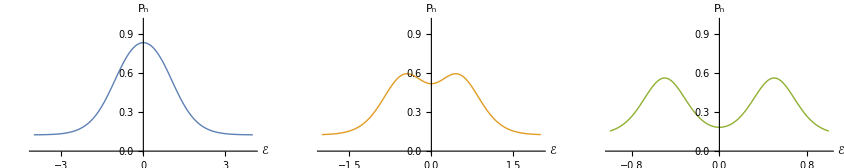
```mathematica
Export["RodeoResolve.svg",-Graphics-];
```

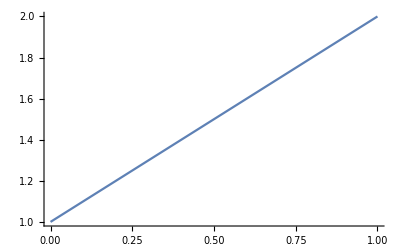

```mathematica
"RandomVariate[BinomialDistribution[shots,1/2^n]]/shots";
"RandomVariate[BinomialDistribution[shots,((1-p)/2)^n+p^n]]/shots";
Plot[Evaluate[((p+(1-p)(1/2)^n)/(1/2^n))/.n->1],{p,0,1}]
```

```mathematica
Series[((p+(1-p)(1/2)^n)/(1/2^n)),{n,Infinity,0}]
```

2^n (2^-n (1-p)+p)

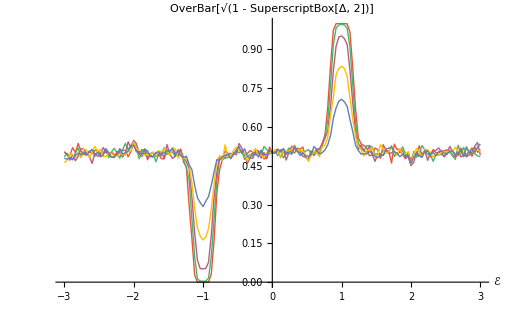

```mathematica
"Table[RodeoPlusOverlapPlot[𝒩Dist,10,n[[1]],1,1/Sqrt[2],1/Sqrt[2],1000,-3,3,1/50,False,n[[2]],False],{n,{{1,RGBColor[0.368417, 0.506779, 0.709798]},{2,RGBColor[0.880722, 0.611041, 0.142051]},{4,RGBColor[0.560181, 0.691569, 0.194885]}}}]";
Show[RodeoPlusOverlapPlot[𝒩Dist,10,16,1,1/Sqrt[2],1/Sqrt[2],1000,-3,3,1/25,True,RGBColor[0.915, 0.3325, 0.2125],False],RodeoPlusOverlapPlot[𝒩Dist,10,8,1,1/Sqrt[2],1/Sqrt[2],1000,-3,3,1/25,True,RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],False],RodeoPlusOverlapPlot[𝒩Dist,10,4,1,1/Sqrt[2],1/Sqrt[2],1000,-3,3,1/25,True,RGBColor[0.736782672705901, 0.358, 0.5030266573755369],False],RodeoPlusOverlapPlot[𝒩Dist,10,2,1,1/Sqrt[2],1/Sqrt[2],1000,-3,3,1/25,True,RGBColor[1, 0.75, 0],False],RodeoPlusOverlapPlot[𝒩Dist,10,1,1,1/Sqrt[2],1/Sqrt[2],1000,-3,3,1/25,True,RGBColor[0.368417, 0.506779, 0.709798],False]]
```

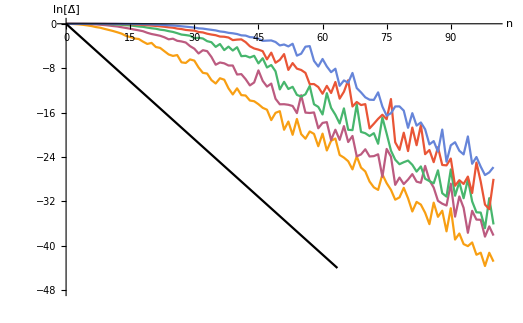

```mathematica
LogOverlapPlot[p_,color_]:=DiscretePlot[Log[Sqrt[Mean[Table[ProbMinus[n,1,1,Sqrt[p],Sqrt[1-p],TimeArray[𝒩Dist,10,n]],{k,2500}]]]],{n,0,100},Filling->None,PlotStyle->color,Joined->True,AxesLabel->{n,"ln[Δ̄]"},PlotRange->{-48,0}];
Show[LogOverlapPlot[1/1000,RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142]],LogOverlapPlot[1/1000000,RGBColor[0.736782672705901, 0.358, 0.5030266573755369]],LogOverlapPlot[1/1000000000,RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]],LogOverlapPlot[1/1000000000000,RGBColor[0.915, 0.3325, 0.2125]],LogOverlapPlot[1/1000000000000000,RGBColor[0.40082222609352647, 0.5220066643438841, 0.85]],Plot[{-Log[2]n},{n,0,100},PlotStyle->{Black},PlotRange->{-44,0}]]
```

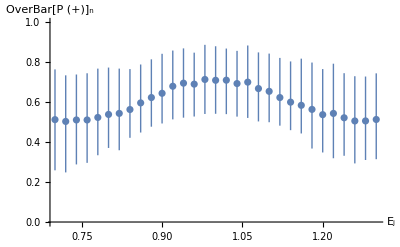
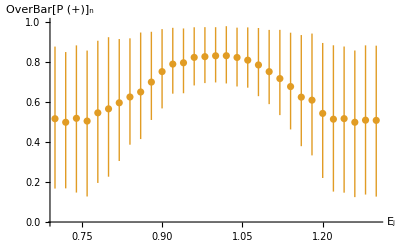
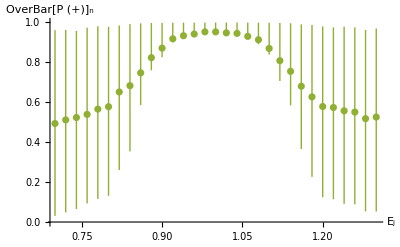

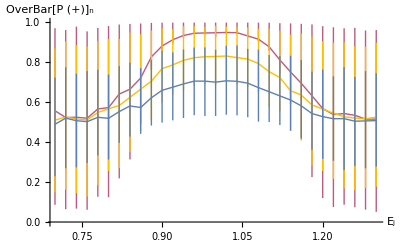

```mathematica
GraphicsRow[Table[RodeoPlusOverlapPlot[𝒩Dist,10,n[[1]],1,1/Sqrt[2],1/Sqrt[2],1000,0.7,1.3,1/50,False,n[[2]],True],{n,{{1,RGBColor[0.368417, 0.506779, 0.709798]},{2,RGBColor[0.880722, 0.611041, 0.142051]},{4,RGBColor[0.560181, 0.691569, 0.194885]}}}]]
"Show[RodeoPlusOverlapPlot[𝒩Dist,10,4,1,1/Sqrt[2],1/Sqrt[2],1000,7/10,13/10,1/50,True,RGBColor[0.736782672705901, 0.358, 0.5030266573755369],True],RodeoPlusOverlapPlot[𝒩Dist,10,2,1,1/Sqrt[2],1/Sqrt[2],1000,7/10,13/10,1/50,True,RGBColor[1, 0.75, 0],True],RodeoPlusOverlapPlot[𝒩Dist,10,1,1,1/Sqrt[2],1/Sqrt[2],1000,7/10,13/10,1/50,True,RGBColor[0.368417, 0.506779, 0.709798],True]]";
```

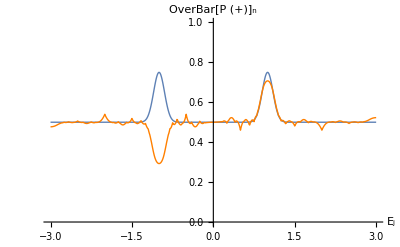

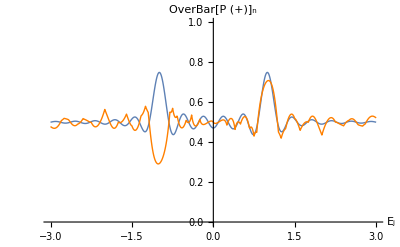

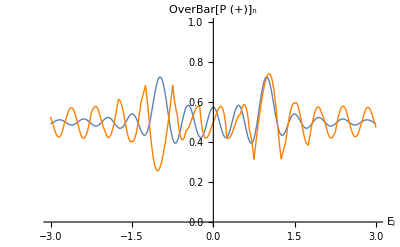

```mathematica
Quiet[RodeoCombinedExpectationPlot[𝒩Dist,10,1,1,1/Sqrt[2],1/Sqrt[2],-3,3,1/100,True,Default,Orange,50,5]]
Quiet[RodeoCombinedExpectationPlot[𝒰Dist,10,1,1,1/Sqrt[2],1/Sqrt[2],-3,3,1/100,True,Default,Orange,50,5]]
Quiet[RodeoCombinedExpectationPlot[𝒜Dist,10,1,1,1/Sqrt[2],1/Sqrt[2],-3,3,1/100,True,Default,Orange,50,5]]
```

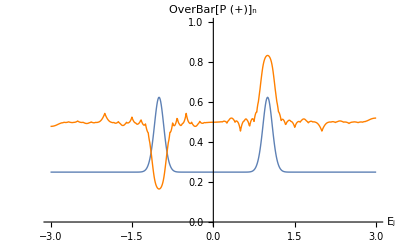

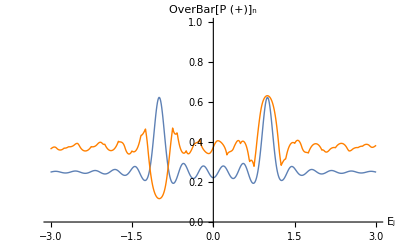

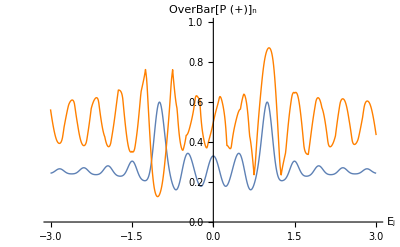

```mathematica
Quiet[RodeoCombinedExpectationPlot[𝒩Dist,10,2,1,1/Sqrt[2],1/Sqrt[2],-3,3,1/100,True,Default,Orange,50,5]]
Quiet[RodeoCombinedExpectationPlot[𝒰Dist,10,2,1,1/Sqrt[2],1/Sqrt[2],-3,3,1/100,True,Default,Orange,50,5]]
Quiet[RodeoCombinedExpectationPlot[𝒜Dist,10,2,1,1/Sqrt[2],1/Sqrt[2],-3,3,1/100,True,Default,Orange,50,5]]
```

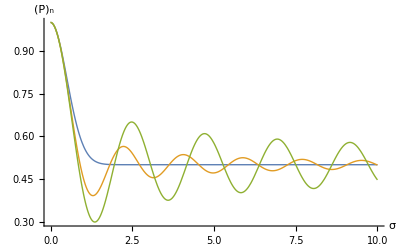

```mathematica
Quiet[Plot[Evaluate[Table[ProbAllZeroExpectation[dist,σ,1,1,-1,1,0],{dist,{𝒩Dist,𝒰Dist,𝒜Dist}}]],{σ,0,10},Filling->None,PlotRange->All,AxesLabel->{"σ","(P̄)_n"},TicksStyle->Directive[FontOpacity->1,FontSize->8],PlotStyle->{Thin,Thin,Thin,Thin}]]
```

```mathematica
GraphicsRow[Quiet[Table[Plot[Evaluate[Table[ProbAllZeroExpectation[dist,σ,n,1,-1,1,0],{n,{1,2,4}}]],{σ,0,10},Filling->None,PlotRange->{0,1},AxesLabel->{"σ","(P̄)_n"},TicksStyle->Directive[FontOpacity->1,FontSize->8],PlotStyle->{Thin,Thin,Thin},PlotLabel->"dist="<>StringTake[ToString[dist],1]],{dist,{𝒩Dist,𝒰Dist,𝒜Dist}}]]]
```

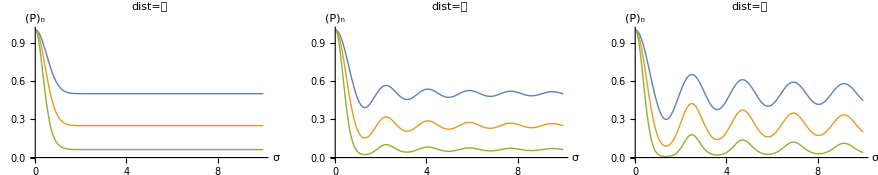
```mathematica
Export["NoiseDists.svg",-Graphics-];
```

```mathematica
Quiet[Table[DiscretePlot[Evaluate[Table[Sqrt[ProbMinusExpectation[dist,σ,n,1,1,1/Sqrt[2],1/Sqrt[2],50,5]],{dist,{𝒩Dist,𝒰Dist,𝒜Dist}}]],{σ,1/20,10,Sqrt[n]/20},Filling->None,PlotRange->All,AxesLabel->{"σ","Δ̄"},PlotLabel->"n="<>ToString[n],TicksStyle->Directive[FontOpacity->1,FontSize->8],Joined->True,PlotStyle->{Thin,Thin,Thin}],{n,{1,2}}]]
```

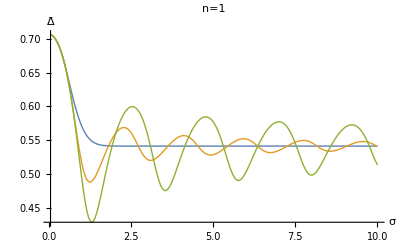
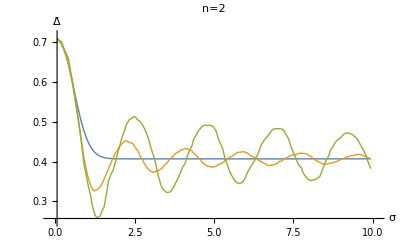
```mathematica
GraphicsRow[{-Graphics-,-Graphics-}]
```

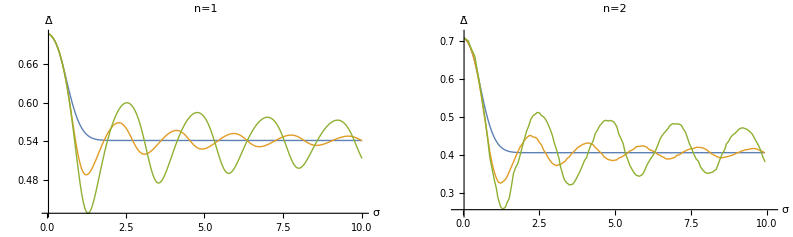
```mathematica
Export["DeltaDists.svg",-Graphics-];
```

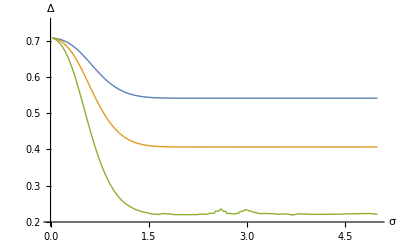

```mathematica
Quiet[DiscretePlot[Evaluate[Table[Sqrt[ProbMinusExpectation[𝒩Dist,σ,n,1,1,1/Sqrt[2],1/Sqrt[2],50,5]],{n,{1,2,4}}]],{σ,Flatten[{Table[k/40,{k,1,120}],Table[3+k/10,{k,1,20}]}]},Filling->None,PlotRange->{1/5,3/4},AxesLabel->{"σ","Δ̄"},TicksStyle->Directive[FontOpacity->1,FontSize->8],Joined->True,PlotStyle->{Thin,Thin,Thin}]]
```

```mathematica
Quiet[DiscretePlot[Evaluate[Table[ProbPlusExpectation[𝒰Dist,σ,n,1,1,1/Sqrt[2],1/Sqrt[2],50,5],{n,{1,2}}]],{σ,1/10,24,1/10},Filling->None,PlotRange->All,AxesLabel->{"σ","P_n"},TicksStyle->Directive[FontOpacity->1,FontSize->8],Joined->True,PlotStyle->{Thin,Thin,Thin}]]
```

```mathematica
GraphicsRow[Quiet[Table[Plot[Evaluate[Table[dist[10,1,ℰ]^n,{dist,{ProbAllZero𝒩,ProbAllZero𝒰,ProbAllZero𝒜}}]],{ℰ,-2,2},PlotRange->{0,1},PlotStyle->{Thin,Thin,Thin},AxesLabel->{"ℰ","(P̄)_n"},PlotLabel->"n="<>ToString[n]],{n,{1,2,4}}]]]
```

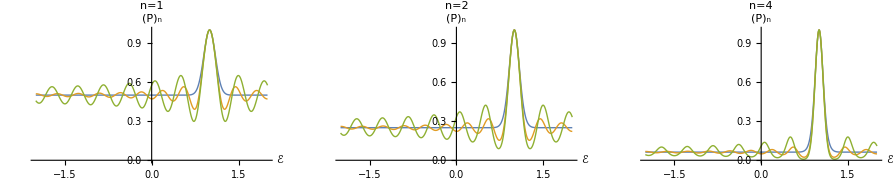
```mathematica
Export["PeakDists.svg",-Graphics-];
```

```mathematica
Quiet[Table[ProbPlusExpectation[𝒩Dist,10,k,1,1,1/Sqrt[2],1/Sqrt[2],50,5],{k,1,5}]]
Quiet[Table[ProbPlusExpectation[𝒰Dist,10,k,1,1,1/Sqrt[2],1/Sqrt[2],50,5],{k,1,5}]]
Quiet[Table[ProbPlusExpectation[𝒜Dist,10,k,1,1,1/Sqrt[2],1/Sqrt[2],50,5],{k,1,5}]]
```

{0.707107,0.834626,0.90917,0.949695,0.99076}

{0.707814,0.632805,0.595532,0.538111,0.472001}

```mathematica
Table[N[1-2^(-k)*(1-1/2)/(1/2+2^(-k)*(1-1/2))],{k,1,5}]
Table[N[1-4^(-k)*(1-1/2)/(1/2+4^(-k)*(1-1/2))],{k,1,5}]
```

{0.666667,0.8,0.888889,0.941176,0.969697}

{0.8,0.941176,0.984615,0.996109,0.999024}

```mathematica
Get["Rubi`"]
```

```mathematica
ℱ𝒮[Int[PDF[𝒩Dist[σ],t]/(1+(β/α)^2(1+Cos[t(ℰ+ω)])/(1+Cos[t(ℰ-ω)])),{t,-∞,∞}]]
ℱ𝒮[Int[PDF[𝒩Dist[σ],t]/(1+(β/α)^2(1+Cos[t(ω+ω)])/(1+Cos[t(ω-ω)])),{t,-∞,∞}]]
ℱ𝒮[Int[PDF[𝒩Dist[σ],t]/(1+(β/α)^2(1+Cos[t(-ω+ω)])/(1+Cos[t(-ω-ω)])),{t,-∞,∞}]]
```

-Limit[Int[(ⅇ^(-t^2/(2 σ^2)))/(1+(β^2 (1+Cos[t (ℰ+ω)]))/(α^2 (1+Cos[t (ℰ-ω)]))),t]/(√(2 π) σ),t→-∞]+Limit[Int[(ⅇ^(-t^2/(2 σ^2)))/(1+(β^2 (1+Cos[t (ℰ+ω)]))/(α^2 (1+Cos[t (ℰ-ω)]))),t]/(√(2 π) σ),t→∞]

-Limit[Int[(2 ⅇ^(-t^2/(2 σ^2)) α^2)/(2+β^2 (-1+Cos[2 t ω])),t]/(√(2 π) σ),t→-∞]+Limit[Int[(2 ⅇ^(-t^2/(2 σ^2)) α^2)/(2+β^2 (-1+Cos[2 t ω])),t]/(√(2 π) σ),t→∞]

-Limit[1/2 Erf[t/(√2 σ)]+(√(2/π) β^2 Int[-(ⅇ^(-t^2/(2 σ^2)))/(1+β^2+α^2 Cos[2 t ω]),t])/σ,t→-∞]+Limit[1/2 Erf[t/(√2 σ)]+(√(2/π) β^2 Int[-(ⅇ^(-t^2/(2 σ^2)))/(1+β^2+α^2 Cos[2 t ω]),t])/σ,t→∞]

```mathematica
ℱ𝒮[Table[StandardDeviation[dist[σ]],{dist,{𝒩Dist,𝒰Dist,𝒜Dist}}]]
```

{σ,σ,σ}

```mathematica
ℱ𝒮[Integrate[PDF[𝒩Dist[σ],t](1+Cos[t(ℰ-ω)])/2,{t,-∞,∞}]]
ℱ𝒮[Integrate[PDF[𝒰Dist[σ],t](1+Cos[t(ℰ-ω)])/2,{t,-∞,∞}]]
ℱ𝒮[Integrate[PDF[𝒜Dist[σ],t](1+Cos[t(ℰ-ω)])/2,{t,-∞,∞}]]
```

1/2 (1+ⅇ^(-1/2 σ^2 (ℰ-ω)^2))

1/6 (3+(√3 Sin[√3 σ (ℰ-ω)])/(ℰ σ-σ ω))

1/2 (1+BesselJ[0,√2 σ (ℰ-ω)])